```mathematica
tf=Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth.tfi","XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
rgbcolors
intensity
bincount=256;
```

{RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}]}

{0.04,0.28,0.5,0.58,0.64,0.7,0.76,0.88,1}

```mathematica
d = Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth.tif","Image3D"];
```

```mathematica
Image3D[d,ColorFunction->rgbafunction]
```

-Graphics3D-

```mathematica
a=Flatten[ImageData[d]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
sum:=Total[h[[2]]];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
op=Module[{t},t=entropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;
op2=entropy[#]&/@intensityfunction//Rescale;
```

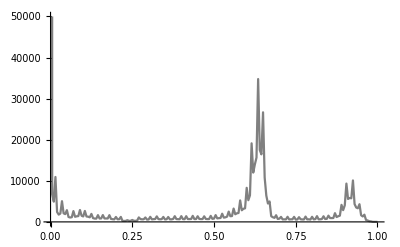

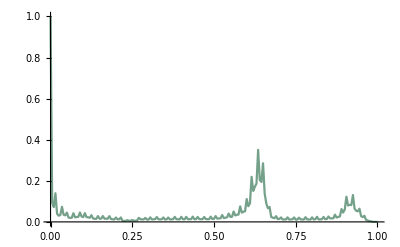

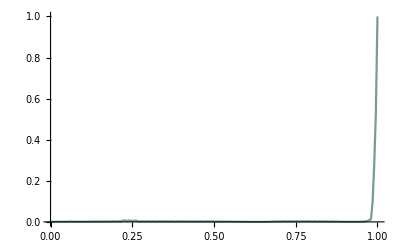

-Graphics-

```mathematica
x=Take[h[[1]],Length[h[[1]]]-1];
y=h[[2]];
acc=Accumulate[y];
ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,50000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
ListLinePlot[Transpose[{intensityfunction,op2}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"intensity transfer function"]
ListLinePlot[Transpose[{intensityfunction,op}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"inverted intensity transfer function"]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"transfer function"]
```

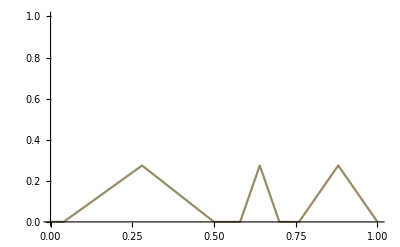

```mathematica
intensity0=intensity;
alpha0=alpha;
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0]];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]
```

```mathematica
ImageDimensions[d]
```

{140,120,161}

```mathematica
(* top *)
list=Image3DSlices[d,All,1];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]
```

161

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth1.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
(* back *)
list=Image3DSlices[d,All,2];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d2a=Image3D[Reverse[list3]];
d2=ImageRotate[d2a,{90 Degree,{1,0,0}}]
```

120

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth2.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
(* left *)
list=Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d3a=Image3D[list3];
d3=ImageRotate[d3a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&
```

140

-Graphics3D-

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth3.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
ImageDimensions[d1]
ImageDimensions[d2]
ImageDimensions[d3]
```

{140,120,161}

{140,120,161}

{140,120,161}

```mathematica
(* bottom *)
list=Reverse@Image3DSlices[d,All,1];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]
```

161

-Graphics3D-

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth4.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
(* front *)
list=Reverse@Image3DSlices[d,All,2];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d5a=Image3D[list3];
d5=ImageRotate[d5a,{90 Degree,{1,0,0}}]
```

120

-Graphics3D-

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth5.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d6a=Image3D[Reverse[list3]];
d6=ImageRotate[d6a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&
```

140

-Graphics3D-

```mathematica
rgblist=Table[ImageApply[List@@rgbfunction[#]&,list[[i]]],{i,1,Length[list]}];
i=1;
tmp=ImageMultiply[list3[[i]],rgblist[[i]]];
acc=Table[tmp=ImageAdd[tmp,ImageMultiply[list3[[i]],rgblist[[i]]]],{i,2,Length[rgblist]}];
result=SetAlphaChannel[Last[acc],Last[list2]]//RemoveAlphaChannel[#,White]&
Export[NotebookDirectory[]<>"tooth6.png",result,ImageSize->1000];
```

-Graphics-

```mathematica
sum=ImageApply[Mean[{##}]&,{d1,d2,d3,d4,d5,d6}]
```

```mathematica
cl=ClusteringComponents[d,4];
```

```mathematica
cl/.{1->0,2->0,3->0}//Colorize
cl/.{1->0,2->0,4->0}//Colorize
cl/.{1->0,3->0,4->0}//Colorize
cl/.{2->0,3->0,4->0}//Colorize
```

```mathematica
seg=Import[#]&/@("D:\\document\\work\\em\\segmentation\\"<>IntegerString[#,10,3]<>".tif"&/@Range[0,160]);
seg3d=Image3D[seg];
```

```mathematica
cl2=ClusteringComponents[seg3d,4];
```

```mathematica
cl2/.{1->0,2->0,3->0}//Colorize
cl2/.{1->0,2->0,4->0}//Colorize
cl2/.{1->0,3->0,4->0}//Colorize
cl2/.{2->0,3->0,4->0}//Colorize
```

```mathematica
part3=ImageApply[If[#2>0,#1,0]&,{sum,Image3D[cl/.{1->0,2->0,3->0}]}]
ImageMeasurements[part3,"TotalIntensity"]//N
```

1714.29

```mathematica
dog=ImageSubtract[GaussianFilter[d,{2,Sqrt[2]/8.*2}],GaussianFilter[d,{4,Sqrt[2]/8.*4}]]
```

```mathematica
bin=MorphologicalComponents[d]//Colorize[#]&;
distance=DistanceTransform[bin]//ImageAdjust;
zero=ImageResize[Image3D[ConstantArray[0,{1,1,1}]],ImageDimensions[d]];
com=ColorCombine[{ImageAdjust[d],distance,zero}];
```

```mathematica
MapIndexed[Export[NotebookDirectory[]<>"tooth\\"<>IntegerString[First[#2],10,3]<>".png",#]&,Image3DSlices[com]];
```

```mathematica
ClusteringComponents[com,3]//Colorize[#-1]&
ClusteringComponents[com,4]//Colorize[#-1]&
```

```mathematica
g=GradientFilter[d,1,Method->"Sobel"]
```

```mathematica
Transpose[{Flatten@ImageData[d],Flatten@ImageData[g]}]//ListPlot[#,PlotRange->{{0,1},{0,1}},PlotLegends->{"Intensity vs gradient magnitude"},PlotStyle->{Orange,Dashed,Thick,Opacity[0.6]}]&
```

```mathematica
{z,y,x}=Dimensions[ImageData[d]]
index=Table[Table[Table[{i,j,k},{k,x}],{j,y}],{i,z}];
flatindex=Flatten[index,2];
flatd=Flatten@ImageData[d];
flatg=Flatten@ImageData[g];
dg=Transpose[{flatd,flatg}];
pos=Position[dg,_?(First[#]>0.2&&First[#]<0.21&),{1},Heads->False];
Length[pos]
```